# Quantum Mechanics

## An introduction to, and derivation of, the fundamental equations of Schrodinger’s quantum mechanics

## Tyson Jones, WSS17 tyson.jones@monash.edu

Note: we’ll work in natural and non-dimensional units where ℏ = m = ω = 1.

## Initialisation

```mathematica
ClearAll["Global`*"]
```

```mathematica
AutoCollapse[] := (
  If[$FrontEnd =!= $Failed, 
   SelectionMove[EvaluationNotebook[], All, GeneratedCell];
   FrontEndTokenExecute["SelectionCloseUnselectedCells"]])
```

```mathematica
colorBar[title_:"arg[ψ]"] :=
	BarLegend[
		{"Rainbow", {-π, π}}, 
		LegendLabel -> title,
		"Ticks" -> {-3.14, -π/2, 0, π/2, 3.14}, 
		"TickLabels" -> {"-π", "-π/2", "0", "π/2", "π"}
	]

colorBarNorm[title_] :=
	BarLegend[
		"Rainbow", 
		LegendLabel -> title
	]

plotWavefunction[psi_, {r_, range__}, showbar_:True, title_:Abs[ψ]^2, legendpsi_:ψ, plotrange_:All, ticks_:Automatic] :=
	ReplaceAll[
		Plot[
			Abs[psi]^2, {r, range}, 
			AxesLabel -> {r, title},
			PlotRange -> plotrange,
			ColorFunction -> (ColorData["Rainbow"][Rescale[Arg[psi /. r -> #], {-π, π}]] &),
			ColorFunctionScaling -> False,
			Ticks -> ticks,
			Filling -> Axis,
			PlotLegends -> If[showbar, colorBarNorm["arg[" <> ToString[legendpsi] <> "] / 2π"], None]
		],
		Line[pts_, _] :> {Black, Line[pts]}
	]
```

```mathematica
simulateWavefunction[psi_, potential_, {r_, domain__}, {_, times__}] :=
	NDSolveValue[
		{ⅈ Derivative[0,1][ψ][r, τ] ==  -Derivative[2,0][ψ][r, τ] / 2 + ψ[r, τ] potential, ψ[r, 0] == psi },
		ψ, 
		{r, domain}, 
		{τ, times},
		Method -> {"FiniteElement"}
	] 
	

Off[NDSolveValue::bcart]
Off[NDSolveValue::femcscd]
```

```mathematica
hamiltonian[psi_, potential_, r_] := 
	-1/2 D[psi, {r,2}] + potential psi
```

```mathematica
expectedEnergy[psi_, potential_,  r_] :=
	Integrate[
		(Conjugate[psi] /. Conjugate[r] -> r)
		(hamiltonian[psi, potential, r]),
		{r, -∞, ∞}
	]
```

```mathematica
quickNormalise[psi_, r_:x] := 
	psi / Sqrt[NIntegrate[
					Abs[psi]^2, {r, -∞, ∞}, 
					Method -> {Automatic, "SymbolicProcessing" -> 0}]]
```

## The Wavefunction

The quantum wavefunction is a (L2 normalizable) complex field defined over some continuous space of states. For example, consider a 1D wavefunction of position:

```mathematica
exampleψ[x_] =  ⅇ^(-(-1+x)^4+2 ⅈ π x)+(ⅇ^(ⅈ ⅇ^(-x^2)-(x-2)^2/2))/π^(1/4) // quickNormalise;
```

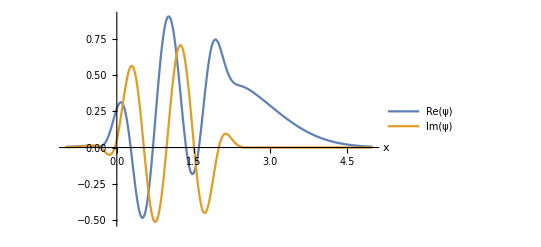

```mathematica
domain = {x, -1, 5};
Plot[
	{Re[exampleψ[x]], Im[exampleψ[x]]}, domain,
	AxesLabel-> {x}, 
	PlotRange -> All,
	PlotLegends-> {Re[ψ], Im[ψ]}
]

AutoCollapse[]
```

Although the wavefunction describes a physical system, it is itself unphysical. Only its absolute value squared can be observed.

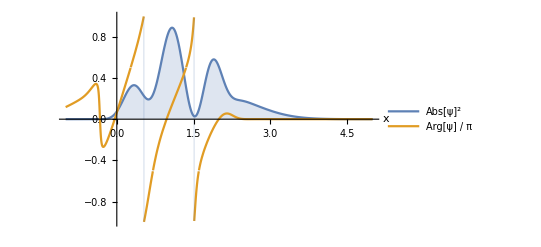

```mathematica
Plot[
	{Abs[exampleψ[x]]^2, Arg[exampleψ[x]]/(π)}, domain,
	AxesLabel-> {x}, 
	PlotRange-> All, 
	Filling -> {1->Axis},
	PlotLegends-> {Abs[ψ]^2, "Arg[ψ] / π"}
]
AutoCollapse[]
```

In the Born interpretation, the absolute value squared of the (normalised) wavefunction is a probability density function. If our wavefunction described a particle’s position, an integrated region of the squared norm would give the probability of finding the particle within that region when measured.

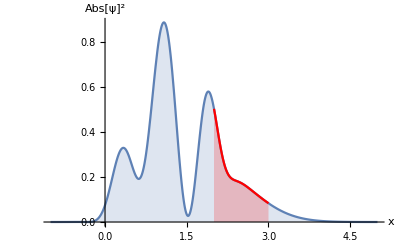
-Graphics-Pr(2 < x < 3) 
= ∫_2^3  |ψ|^2 ⅆx 
= 0.196048

```mathematica
Overlay[{
	Plot[{
			Abs[exampleψ[x]]^2, 
			ConditionalExpression[Abs[exampleψ[x]]^2, x > 2 && x < 3]
		}, 
		domain,
		Filling -> Axis,
		AxesLabel-> {x, Abs[ψ]^2},
		PlotStyle -> {Default, Red},
		PlotRange-> All
	],
	Text["Pr(2 < x < 3) \n= ∫_2^3  |ψ|^2 ⅆx \n= " <>
		 ToString[NIntegrate[Abs[exampleψ[x]]^2, {x, 2, 3}]]]
	},
	Alignment -> {0.6, 0}
]
AutoCollapse[]
```

Alternatively, if we measured the position of many particles all described by the same wavefunction, we’d expect the distribution to follow the norm squared of that wavefunction.

```mathematica
exampleSamples = RandomVariate[ProbabilityDistribution[Abs[exampleψ[x]]^2, {x, -∞, ∞}], 10^3];
```

```mathematica
Animate[
	Overlay[{
	Show[
		Plot[{
					Abs[exampleψ[x]]^2, 
					ConditionalExpression[Abs[exampleψ[x]]^2, x > 2 && x < 3]},
				domain, 
				Filling-> Axis, 
				PlotStyle->{Default, Red}, 
				PlotRange->{0,1}
			],
			Histogram[
				exampleSamples[[;;n]], 
				{0.1}, 
				Function[{bins, counts}, counts/0.1/Length[exampleSamples]]
			],
			Histogram[
				Select[exampleSamples[[;;n]], 2 < # ≤ 3 &], 
				{0.1}, 
				Function[{bins, counts}, counts/0.1/Length[exampleSamples]],
				ChartStyle-> RGBColor[1, 0.3, 0.3]
			],
		AxesLabel -> {"x", Abs[ψ]^2}, 
			PlotRange -> {0, 1}
	],
		Text[
			"# measurements ∈ [2, 3] \n=" <>
			StringTake[
				ToString[
					100 N[Count[exampleSamples[[;;n]], u_ /; (u > 2 && u < 3)] / If[n > 0, n, 1]]
				], UpTo[4]
			] <> "%"
		]},
		Alignment -> {1, 0}],
	{{n, 0, "# measurements"}, 0, Length[exampleSamples], 1}
]

AutoCollapse[]
```

The probability density function alone however is an incomplete description of the system. The complex phase is very important; we’ll here-forth indicate it by colour.

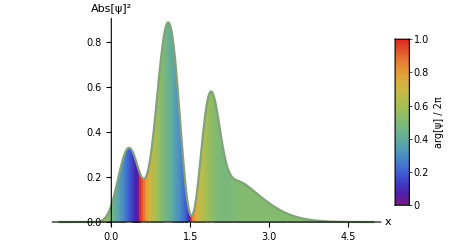

```mathematica
plotWavefunction[exampleψ[x], domain]
```

The complex phase, together with the amplitude, governs the evolution of the wavefunction in time. A phase gradient indicates a probability current; that the probability density function (and the likelihood our particle will appear in a given region) will change in time.

```mathematica
exampleψ[space_, time_] =
	simulateWavefunction[exampleψ[x], 0, {x, -2, 8}, {t, 0, 0.3}][space, time];
```

```mathematica
Animate[
	Overlay[
		{Show[
			plotWavefunction[exampleψ[x, t], domain, False],
			Plot[Abs[exampleψ[x, t]]^2,
				{x, 2, 3}, Filling -> Axis,
				PlotRange -> {0, 1.2},
				PlotStyle -> Red],
			PlotRange -> {0, 1.2}],
		 Text[
			Style[
				"Pr(2 < x < 3) \n= " <>
				ToString[NIntegrate[
					Abs[exampleψ[x, t]]^2, 
					{x, 2, 3},
					Method -> {Automatic, "SymbolicProcessing" -> 0}
				]], 
				Black]]},
		Alignment->{0.8, 0}],
	{t, 0, 0.3},
	SaveDefinitions->True
] // 
	Legended[#, colorBar[]]&


AutoCollapse[]
```

This was an example of a free system, in no external potential. Its evolution, and the evolution of general trapped systems, is determined by the Schrodinger equation.

## The Schrodinger Equation

### Time dependent and independent forms

For a wavefunction ψ[r,t] with total energy encoded in a Hamiltonian operator Ĥ, the time-dependent Schrodinger equation is

```mathematica
schrodEq[ψ_] = 
	ⅈ Derivative[0,1][ψ][r,t]==Ĥ[ψ[r,t]];
```

where r can represent one or more spatial dimensions.

We can often produce an infinite set of eigenfunctions ϕ[r,t] (with eigenvalues Ε) of the Hamiltonian, which each satisfy

```mathematica
schrodEq[ϕ] /. Ĥ[ϕ[r,t]] ->  Ε ϕ[r,t]
```

ⅈ ϕ^(0,1)[r,t]==Ε ϕ[r,t]

and which can be expressed in terms of a time-independent eigenfunction ϕ[r] and an oscillator time component.

```mathematica
eigTimeForm[ϕ_] =
	ϕ[r, t] -> DSolveValue[%, ϕ[r, t], {r, t}]  /. C[1] -> ϕ
```

ϕ[r,t]→ⅇ^(-ⅈ t Ε) ϕ[r]

Returning this form to the Schrodinger equation gives

```mathematica
schrodEq[ϕ] /. {%, D[%,t]}
```

ⅇ^(-ⅈ t Ε) Ε ϕ[r]==Ĥ[ⅇ^(-ⅈ t Ε) ϕ[r]]

which for a linear and time-independent Hamiltonian, presents the time-independent Schrodinger equation of the energy eigenfunctions ϕ[r]

```mathematica
eigfGeneralEq[ϕ] =
% /. Ĥ[c__ ϕ[r]] -> c Ĥ[ϕ[r]] // 
	Simplify[#, Assumptions-> {t>0, Ε>0}]&
```

Ε ϕ[r]==Ĥ[ϕ[r]]

### Operators and eigenfunctions

For a single particle in a scalar external potential V described in a non-inertial, non-relativistic frame, the Hamiltonian takes the form

```mathematica
hamiltonianSub =
	Ĥ[ψ_] :> -1/2 Laplacian[ψ, {r}] + V [r]ψ
```

Ĥ[ψ_]:>-(ψ{r})/2+V[r] ψ

where the Laplacian gives an analog of kinetic energy. The time-dependent Schrodinger equation becomes

```mathematica
schrodEq[ψ]  /. hamiltonianSub
```

ⅈ ψ^(0,1)[r,t]==V[r] ψ[r,t]-1/2 ψ^(2,0)[r,t]

and the time-independent Schrodinger equation of the eigenfunctions becomes

```mathematica
eigfEq[ϕ_] =
	eigfGeneralEq[ϕ] /. hamiltonianSub
```

Ε ϕ[r]==V[r] ϕ[r]-ϕ''[r]/2

Every possible wavefunction instance of the system can be constructed from a linear superposition of the eigenfunctions ϕ_n,

```mathematica
ψ[r] -> Sum[Subscript[c, n] Subscript[ϕ, n][r], {n, 0, ∞}]
```

ψ[r]→∑_(n=0)^∞ c_n ϕ_n[r]

each of which merely evolve in time by a complex oscillation at a rate proportional to their energy eigenvalues Ε_n.

```mathematica
eigTimeForm[Subscript[ϕ, n]] /. Ε -> Subscript[Ε, n]
```

ϕ_n[r,t]→ⅇ^(-ⅈ t Ε_n) ϕ_n[r]

Since the Schrodinger equation is linear, the total wavefunction evolves like the sum of the simple eigenfunction dynamics,

```mathematica
ψ[r, t] ->  ∑_(n=0)^∞ Subscript[c, n] Subscript[ϕ, n][r, t] /. %
```

ψ[r,t]→∑_(n=0)^∞ ⅇ^(-ⅈ t Ε_n) c_n ϕ_n[r]

where (normalised) c_n are trivially found by projecting the initial wavefunction ψ[r, 0] onto the orthonormal set {n:ϕ_n}, having first calculated the spectrum of the particular Hamiltonian.

The quantum harmonic oscillator is an example of a simple Hamiltonian system with an interesting family of eigenfunctions, which can be used to propagate a wavefunction through time without numerically solving the time-dependent Schrodinger equation.

## The Quantum Harmonic Oscillator

### Finding the eigenfunctions

Consider a simple one-dimensional quadratic trapping potential.

```mathematica
harmonicV[x_] = 1/2 x^2;
```

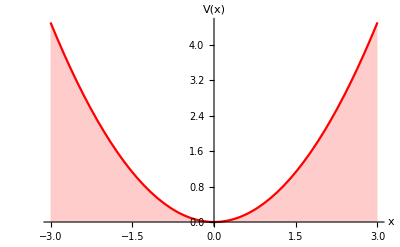

```mathematica
Plot[harmonicV[x], {x, -3, 3}, Filling -> Axis, AxesLabel-> {x, V[x]}, PlotStyle-> Red]
AutoCollapse[]
```

The corresponding time-independent Schrodinger equation is

```mathematica
eigfEq[Subscript[ϕ, n]] /. {r -> x, Ε -> Subscript[Ε, n], V[r] -> harmonicV[x]}
```

Ε_n ϕ_n[x]==1/2 x^2 ϕ_n[x]-1/2 ϕ_n''[x]

which is solved for the energy eigenfunctions ϕ_n and eigenvalues Ε_n.

```mathematica
DSolveValue[% , Subscript[ϕ, n][x], x]
```

C[2] ParabolicCylinderD[1/2 (-1-2 Ε_n),ⅈ √2 x]+C[1] ParabolicCylinderD[1/2 (-1+2 Ε_n),√2 x]

Our problem is underspecified, with two arbitrary constants (C[1] and C[2]) and one normalisation condition (∫|ϕ_n|^2 dx = 1). The representation of the energy eigenfunction-basis is therefore not unique. We’ll arbitrarily pick one that’s entirely real.

```mathematica
oscillatorϕ[n_] =
	% /. C[2] -> 0 // FunctionExpand
```

2^(1/4 (1-2 Ε_n)) ⅇ^(-x^2/2) C[1] HermiteH[1/2 (-1+2 Ε_n),x]

Since Hermite polynomials must have integer degree, we’ve found the discretized energy eigenvalues.

```mathematica
n == Cases[%, HermiteH[n_, __] -> n][[1]]  //  Solve[#, Subscript[Ε, n]] &
```

{{Ε_n→1/2 (1+2 n)}}

```mathematica
oscillatorϕ [n_] = oscillatorϕ[n] /. %[[1]]
```

2^(-n/2) ⅇ^(-x^2/2) C[1] HermiteH[n,x]

Finally, we solve for C[1] by asserting normalisation. Analytic solution is expensive, even for particular n; we’ll instead employ numerical approximation.

```mathematica
oscillatorϕ[n_] = oscillatorϕ[n] /. C[1] -> 1;
oscillatorϕ[n_, r_] :=  quickNormalise[oscillatorϕ[n]] /. x -> r
```

```mathematica
Legended[
	Manipulate[
		Show[
		plotWavefunction[oscillatorϕ[n, x], {x, -5, 5},False, Abs[Subscript[ϕ, n]]^2, "ϕ" <> ToString[n], {0,0.6}],
			Plot[
			harmonicV[x]/25,
				{x, -5, 5}, 
				PlotStyle->{Thick, Red},
				Filling -> Axis
		]
		],
	{{n,0}, 0, 15, 1}
	], 
	colorBar["arg[ϕn]"]
]
AutoCollapse[]
```

### Superposing the eigenfunctions

We found earlier that energy eigenfunctions of any system merely oscillate in phase through time at a rate proportional to their energy (∝ n) ; their probability density functions remain fixed. We can now demonstrate this for the quantum harmonic oscillator.

```mathematica
oscillatorϕ[n_, x_, t_] := oscillatorϕ[n, x] ⅇ^(-ⅈ t Ε) /. Ε -> 1/2 (1+2 n)
```

```mathematica
Legended[
	Manipulate[
		Animate[
			Show[
				plotWavefunction[oscillatorϕ[n, x, t], {x, -5, 5}, False, Abs[Subscript[ϕ, n]]^2],
				Plot[
				harmonicV[x]/25,
					{x, -5, 5}, 
					PlotStyle->{Thick, Red},
					Filling -> Axis
			]
			],
			{t, 0, 4π}
		],
		{n, 0, 15,1}
	],
	colorBar[Arg[ϕn]]
]
AutoCollapse[]
```

Mixing out-of-phase eigenfunctions will introduce phase gradients...

```mathematica
oscillatorϕ[1, x] + ⅇ^(-π/4 ⅈ) oscillatorϕ[2, x] + ⅇ^(π/3 ⅈ)oscillatorϕ[9, x]   // quickNormalise;
```

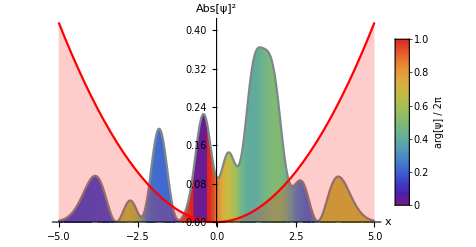

```mathematica
Show[
	plotWavefunction[% , {x, -5, 5}],
	Plot[
		harmonicV[x]/30,
		{x, -5, 5}, 
		PlotStyle->{Thick, Red},
		Filling -> Axis
	]
]
AutoCollapse[]
```

which are otherwise induced in-time by mixing in-phase eigenfunctions, due to their different eigenvalues.

```mathematica
oscillatorϕ[2, x, t] + oscillatorϕ[3, x, t]  ;
```

```mathematica
Legended[
	Animate[
	Show[
		plotWavefunction[%, {x, -5, 5}, False], 
		Plot[
			harmonicV[x]/15,
			{x, -5, 5}, 
			PlotStyle->{Thick, Red},
			Filling -> Axis
		],
			PlotRange-> {0, 1.2}
	],
	{t, 0, 4π}
	],
	colorBar[]
]
AutoCollapse[]
```

These examples (composed of a finite number of eigenfunctions) are periodic at some multiple of π. Even finite superpositions can lead to complicated (but periodic) evolution.

```mathematica
ψ->∑_(n=0)^(number of modes) ⅇ^(-ⅈ t Subscript[Ε, n]) Subscript[c, n] Subscript[ϕ, n][r];
```

```mathematica
maxModes = 15;

manipulateCoeffs[{coeffs__}, exp_] := 
	Manipulate[
		Animate[
			plotWavefunction[exp, {x, -5, 5}, False, Abs[ψ]^2, ψ, All, None],
			{t, 0, 4π}
		],
		Style["complex coefficients\n"],
		coeffs,
		ControlPlacement->Left
	]


Manipulate[
	manipulateCoeffs[
		Table[
			{{c[n],If[n==0,{1,0},{0,0}], Subscript[c, n]}, {-1,-ⅈ}, {1,ⅈ}},
			{n, 0, numModes-1}
		],
		Sum[c[n] . {oscillatorϕ[n, x, t], 
				    oscillatorϕ[n, x, t]},     (* stupid hack; can't unpack c[n] early! *)
			{n, 0, numModes-1}]
		],     
	{{numModes,4,"number of modes"}, 1, maxModes, 1}
]

AutoCollapse[]
```

By forming a complete, orthonormal basis, the energy eigenfunctions can be linearly superposed to produce any possible wavefunction, though this generally requires non-zero coefficients of an infinite number of them (a rather hard computation).

### Coherent States

A coherent wavefunction is one which maintains its probability density profile in time while still translating in space.

```mathematica
coherentTime  = 4π;
coherentψ[x_] = oscillatorϕ[0, x - 1] // quickNormalise;
coherentψ[space_, time_] =
	simulateWavefunction[coherentψ[x], harmonicV[x], {x, -5,5}, {t, 0, coherentTime}][space, time];
	
Legended[
	Animate[
		Show[
			plotWavefunction[
				coherentψ[x, t], 
				{x, -4, 4}, 
				False],
			Plot[
				harmonicV[x]/15,
				{x, -4, 4}, 
				PlotStyle->{Thick, Red},
				Filling -> Axis
			],
			PlotRange -> {0, 0.8}
		],
		{t, 0, coherentTime}
	], 
	colorBar[]
]
AutoCollapse[]
```

We created the above (due to numerical imprecision; approximate) coherent wavefunction of the quantum harmonic oscillator by translating the lowest energy eigenfunction (the “ground-state”) out of the trap minimum.

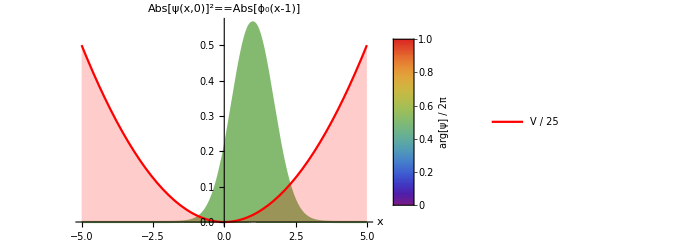

```mathematica
Show[
	plotWavefunction[coherentψ[x], {x, -5, 5}, True, Abs[ψ[x,0]]^2 == Abs[Subscript[ϕ, 0][x-1]]],
	Plot[harmonicV[x]/25, 
		{x, -5, 5}, 
		Filling -> Axis, 
		AxesLabel-> {x, V[x]}, 
		PlotStyle-> Red,
		PlotLegends -> {"V / 25"}
	]
]
AutoCollapse[]
```

The coherent states require an infinite number of terms to represent analytically, in either eigenfunction or coordinate representation.

```mathematica
coherentϕ[α_, x_] = ⅇ^(-1/2 Abs[α]^2) ∑_(n=0)^∞ (α^n Subscript[ϕ, n][x])/(√(n!))   /. Subscript[ϕ, n_][x] -> oscillatorϕ[n]
```

ⅇ^(-1/2 Abs[α]^2) ∑_(n=0)^∞ (2^(-n/2) ⅇ^(-x^2/2) α^n HermiteH[n,x])/(√(n!))

## Quantum Tunneling

The Schrodinger evolution of the wavefunction enables particles to be appear in classically forbidden regions. Consider some corresponding waveform ∝ e^(-2 x^2), kicked by a phase gradient e^(ⅈ x), approaching a potential barrier.

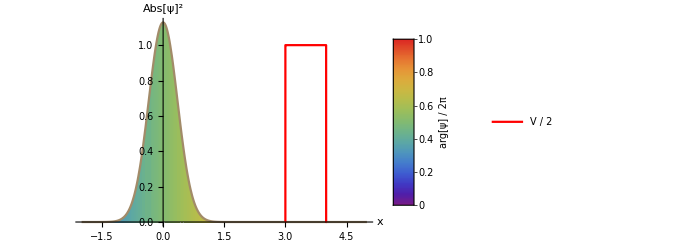

```mathematica
incidentψ[x_] = (√2)/π^(1/4)Exp[- 2 x^2]Exp[ ⅈ x]; 
stepHeight = 2;
stepV[x_] = stepHeight (UnitStep[x-3] - UnitStep[x-4]);

Show[
	plotWavefunction[ incidentψ[x], {x, -2, 5} ],
	Plot[
		stepV[x]/stepHeight, 
		{x,2.99, 4.01}, 
		Exclusions->None, 
		PlotStyle->{Thick, Red},
		PlotLegends->{"V / " <> ToString[stepHeight]}]
]
AutoCollapse[]
```

This wavefunction has an expectation energy much smaller than the height of the potential.

```mathematica
expectedEnergy[incidentψ[x], 0, x]
```

3/2

In a classical analog, this would mean the particle cannot be found beyond the potential barrier. However, when we evolve the wavefunction through time...

```mathematica
endTime = 1.8;
incidentψ[space_, time_] =
	simulateWavefunction[incidentψ[x], stepV[x], {x, -6, 12}, {t, 0, endTime}][space, time];
```

```mathematica
Animate[
	Show[
		plotWavefunction[
			incidentψ[x, t], 
			{x, -3, 8}, 
			False],
		Plot[
			stepV[x]/stepHeight,{x,2.99, 4.01}, Exclusions->None, PlotStyle->{Thick, Red}
		],
		PlotRange -> {0, 1.2}
	],
	{t, 0,endTime}
] // Legended[#, colorBar[]]&
AutoCollapse[]
```

we find a non-negligible wavefunction amplitude can emerge beyond the barrier, after exponentially decaying within. The wavefunction has partially reflected off of, and partially transmitted through, the barrier.

```mathematica
transmittedψ[x_] = incidentψ[x, endTime];
transmittedGrid = Range[-3, 8, 0.01];
transmittedProbs = (Abs[transmittedψ[#1]]^2 &) @ transmittedGrid;
transmittedSamples = RandomVariate[EmpiricalDistribution[ transmittedProbs -> transmittedGrid], 10^3];
```

This implies a possibility of measuring the particle beyond the classically insurmountable barrier.

```mathematica
Animate[
	Overlay[{
	Show[
		Plot[{
					Abs[transmittedψ[x]]^2, 
					ConditionalExpression[Abs[transmittedψ[x]]^2, x > 4]},
				{x, -3, 8}, Filling-> Axis, PlotStyle->{Default, Red}, PlotRange->{0,0.5}
			],
			Histogram[
				transmittedSamples[[;;n]], {0.2}, 
				Function[{bins, counts}, counts/0.2/Length[transmittedSamples]]
			],
			Histogram[
				Select[transmittedSamples[[;;n]], # > 4 &], {0.2}, 
				Function[{bins, counts}, counts/0.2/Length[transmittedSamples]],
				ChartStyle-> RGBColor[1, 0.3, 0.3]
			],
			Plot[
			stepV[x] 0.5 / stepHeight,{x,2.99, 4.01}, Exclusions->None, PlotStyle->{Thick, Red}
		],
			AxesLabel -> {"x", (Abs[ψ]^2)[Subscript[t, final]]}, PlotRange -> {0, 0.5}
	],
		Text[
			"# measurements > 4 \n=" <>
			StringTake[
				ToString[
					100 N[Count[transmittedSamples[[;;n]], u_ /; (u > 4)] / If[n > 0, n, 1]]
				], UpTo[4]] <> "%"
		]},
		Alignment -> {1, 0}],
	{{n, 0, "# measurements"}, 0, Length[transmittedSamples], 1}
]
AutoCollapse[]
```